```mathematica
Needs["Cosmology`EH98`"];
Needs["Cosmology`Defs`"];
Needs["LevelScheme`"];
```

```mathematica
SetDirectory["~/myWork/np_sandbox/WFIRST_SDT_0512"];
```

## nP calculations for WFIRST SDT

#### Start by estimating P(k)

We have a choice on what k to estimate nP at and k=0.14 might be a better choice, but for now, we stick to k=0.2

```mathematica
kcen=0.2;
```

```mathematica
pk1[k_] := pkEH[k, 0.96, 3. 10^-9, FoMSWG];
```

```mathematica
s8 = sigmaR[pk1]
```

0.724952

```mathematica
P0 = pk1[kcen] * (0.8/s8)^2
```

1795.24

```mathematica
hubble0 = Hubble[1.0, FoMSWG]
```

0.719027

## Define volumes

```mathematica
perdeg2 = (Pi/180.0)^2;
```

#### Simple volume formula -- assume a flat Universe

```mathematica
volZbin[zmin_, zmax_, cosmo_?OptionQ]:= Module[{r1, r2, h}, 
r1 = comdis[z2a[zmin], cosmo];
r2 = comdis[z2a[zmax], cosmo];
h = Hubble[1.0, cosmo];
perdeg2 * (r2^3 - r1^3)/3.0 * (3000.0)^3 * h^3
];
```

## Bias

```mathematica
bias[z_, off_:0.0] := off + 0.9 + 0.4*z;
```

```mathematica
Dgrowth0 = Dgrowth[1.0, FoMSWG]
```

0.750975

```mathematica
biasBB[z_ , norm_] := norm * Dgrowth0/Dgrowth[z2a[z], FoMSWG];
```

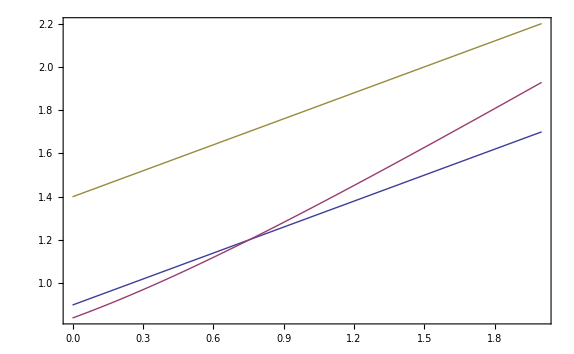

```mathematica
Plot[{bias[z], biasBB[z, 0.84], bias[z, 0.5]}, {z, 0, 2.0}, 
Frame->True]
```

## Redshift distributions

#### WFIRST

```mathematica
wfirstZin = Import["drm1_zsurvey_060712.txt", "Table"];
```

```mathematica
wfirstZin // TableForm
```

1.35 | 3.77
1.45 | 3.73
1.55 | 3.55
1.65 | 3.28
1.85 | 2.84
1.95 | 2.89
2.05 | 2.97
2.15 | 3.07
2.25 | 3.01
2.35 | 2.58
2.45 | 2.16
2.55 | 1.66
2.65 | 1.25

```mathematica
process[ll_, fac_:1.0] := Module[{z0, zmin, zmax, n1, v1, dz, nP1, nP2, nbar},
z0 = ll[[1]];
zmin = z0-0.05;
zmax = z0 + 0.05;
v1 = volZbin[zmin, zmax, FoMSWG];
nbar = ll[[2]]*fac/hubble0^3;
dz = Dgrowth [z2a[z0], FoMSWG]/Dgrowth0;
nP1 = (dz*bias[z0])^2*P0*nbar;
nP2 = (dz*bias[z0, 0.5])^2 * P0 * nbar;
{z0, v1,nbar ,nP1, nP2}
];
```

```mathematica
wfirstnp = process[#, 10^-4] &/@ wfirstZin;
```

```mathematica
wfirstnp // TableForm
```

1.35 | 393803. | 0.00101416 | 1.12392 | 2.03992
1.45 | 411632. | 0.0010034 | 1.0897 | 1.95035
1.55 | 426924. | 0.000954976 | 1.01707 | 1.79624
1.65 | 439896. | 0.000882344 | 0.922229 | 1.60814
1.85 | 459743. | 0.000763981 | 0.770752 | 1.31236
1.95 | 467027. | 0.000777431 | 0.771377 | 1.29886
2.05 | 472801. | 0.000798952 | 0.780168 | 1.29968
2.15 | 477235. | 0.000825853 | 0.79417 | 1.3095
2.25 | 480483. | 0.000809712 | 0.767279 | 1.25275
2.35 | 482684. | 0.000694039 | 0.648447 | 1.04875
2.45 | 483962. | 0.000581056 | 0.535576 | 0.85834
2.55 | 484431. | 0.000446552 | 0.406276 | 0.645431
2.65 | 484189. | 0.000336259 | 0.302128 | 0.475937

#### Euclid

```mathematica
euclidZin  = Import["euclid_v2.txt", "Table"];
```

```mathematica
euclidZin // TableForm
```

0.7 | 0.000143
0.75 | 0.000159
0.8 | 0.000176
0.85 | 0.000186
0.9 | 0.000168
0.95 | 0.000151
1. | 0.000135
1.05 | 0.00012
1.1 | 0.000107
1.15 | 0.0000941
1.2 | 0.0000774
1.25 | 0.0000548
1.3 | 0.0000556
1.35 | 0.0000556
1.4 | 0.0000553
1.45 | 0.0000543
1.5 | 0.0000521
1.55 | 0.0000495
1.6 | 0.000047
1.65 | 0.0000443
1.7 | 0.0000419
1.75 | 0.0000396
1.8 | 0.0000375
1.85 | 0.0000355
1.9 | 0.0000337
1.95 | 0.0000315
2. | 0.0000294

```mathematica
euclidnp = process /@ euclidZin;
```

```mathematica
euclidnp // TableForm
```

0.7 | 207167. | 0.000384681 | 0.493358 | 1.00004
0.75 | 225674. | 0.000427722 | 0.542177 | 1.08812
0.8 | 243637. | 0.000473453 | 0.593155 | 1.17898
0.85 | 260979. | 0.000500354 | 0.619568 | 1.21996
0.9 | 277642. | 0.000451932 | 0.553132 | 1.07923
0.95 | 293584. | 0.000406201 | 0.491443 | 0.95037
1. | 308776. | 0.00036316 | 0.43436 | 0.832737
1.05 | 323202. | 0.000322809 | 0.38174 | 0.72571
1.1 | 336856. | 0.000287838 | 0.336589 | 0.634638
1.15 | 349738. | 0.000253136 | 0.292751 | 0.547579
1.2 | 361859. | 0.000208212 | 0.238183 | 0.442047
1.25 | 373231. | 0.000147416 | 0.166833 | 0.30728
1.3 | 383872. | 0.000149568 | 0.167488 | 0.306203
1.35 | 393803. | 0.000149568 | 0.165756 | 0.300848
1.4 | 403048. | 0.000148761 | 0.163185 | 0.294095
1.45 | 411632. | 0.000146071 | 0.158634 | 0.283925
1.5 | 419582. | 0.000140153 | 0.150715 | 0.267938
1.55 | 426924. | 0.000133159 | 0.141816 | 0.250462
1.6 | 433687. | 0.000126433 | 0.133383 | 0.234056
1.65 | 439896. | 0.00011917 | 0.124557 | 0.217197
1.7 | 445581. | 0.000112714 | 0.11674 | 0.202317
1.75 | 450766. | 0.000106527 | 0.10935 | 0.188373
1.8 | 455478. | 0.000100878 | 0.102649 | 0.175791
1.85 | 459743. | 0.0000954976 | 0.096344 | 0.164046
1.9 | 463585. | 0.0000906555 | 0.0906933 | 0.153556
1.95 | 467027. | 0.0000847373 | 0.0840774 | 0.141571
2. | 470091. | 0.0000790882 | 0.0778416 | 0.130365

#### BigBOSS

```mathematica
bbIn = Drop[Import["bb_smooth_v2.txt", "Table"],2];
```

```mathematica
bbIn//TableForm
```

0.15 | 376 | 50 | 8
0.25 | 347 | 125 | 23
0.35 | 291 | 222 | 31
0.45 | 285 | 332 | 31
0.55 | 431 | 448 | 32
0.65 | 722 | 563 | 34
0.75 | 1112 | 675 | 37
0.85 | 1333 | 471 | 44
0.95 | 1401 | 91 | 50
1.05 | 1469 | 11 | 56
1.15 | 1483 | 0 | 62
1.25 | 1421 | 0 | 69
1.35 | 1120 | 0 | 75
1.45 | 775 | 0 | 81
1.55 | 460 | 0 | 83
1.65 | 179 | 0 | 80
1.75 | 49 | 0 | 77
1.85 | 0 | 0 | 74
1.95 | 0 | 0 | 71

```mathematica
processBB[ll_] := Module[{z0, zmin, zmax, n1, v1, dz, nP, nPtot, nbar}, 
z0 = ll[[1]];
zmin = z0-0.05;
zmax = z0 + 0.05;
n1 = ll[[2]] * 0.1;
v1 = volZbin[zmin, zmax, FoMSWG];
nbar = n1/v1;
dz = Dgrowth [z2a[z0], FoMSWG]/Dgrowth0;
nP = (dz*bias[z0])^2*P0*nbar;
nPtot = (ll[[2]]*0.84^2  + ll[[3]]*1.7^2 + ll[[4]]*1.2^2)*P0*0.1/v1;
{z0, v1, nbar, nP, nPtot}
];
```

```mathematica
bbnp = processBB /@ bbIn;
```

```mathematica
bbnp // TableForm
```

0.15 | 16804.6 | 0.00223749 | 3.20613 | 4.50103
0.25 | 41821.2 | 0.000829723 | 1.17089 | 2.74392
0.35 | 74172.4 | 0.000392329 | 0.543563 | 2.15787
0.45 | 110874. | 0.000257049 | 0.348878 | 1.95145
0.55 | 149506. | 0.000288283 | 0.382735 | 1.97518
0.65 | 188217. | 0.0003836 | 0.497735 | 2.08453
0.75 | 225674. | 0.000492747 | 0.624602 | 2.21838
0.85 | 260979. | 0.000510769 | 0.632465 | 1.62693
0.95 | 293584. | 0.000477206 | 0.577348 | 0.80933
1.05 | 323202. | 0.000454515 | 0.53749 | 0.638192
1.15 | 349738. | 0.000424031 | 0.490391 | 0.582957
1.25 | 373231. | 0.00038073 | 0.430879 | 0.53007
1.35 | 393803. | 0.000284406 | 0.315187 | 0.409497
1.45 | 411632. | 0.000188275 | 0.204468 | 0.289361
1.55 | 426924. | 0.000107747 | 0.114753 | 0.186745
1.65 | 439896. | 0.0000406914 | 0.0425308 | 0.0985583
1.75 | 450766. | 0.0000108704 | 0.0111585 | 0.0579292
1.85 | 459743. | 0. | 0. | 0.0416103
1.95 | 467027. | 0. | 0. | 0.0393008

## Plot

```mathematica
SetOptions[Figure, ImageSize-> 72*{18,12}];
```

```mathematica
fig = Figure[{
SetOptions[FigurePanel, FontFamily-> "Times", FontSize-> 35],
FigurePanel[
{{0,1},{0,1}},
Frame->True,
PlotRange-> {{0.5,2.7}, {0.0, 2.5}},
FrameTicks->{LinTicks[0.5, 2.7], 
                         LinTicks[0.0, 2.5], 
                         LinTicks[0.5, 2.7], 
		       LinTicks[0.0, 2.5]},
ExtendRange-> 0.0, 
TickNudge->{{0,-3},{-3,0},0,0},
LabB -> "Redshift",BufferB->3.5, 
LabL->"n P(k=0.2)", BufferL->4.0
],
SetOptions[DataLine, ShowLine->True],
SetOptions[DataSymbol, SymbolSize-> 10],
(*DataPlot[ bbnp[[All,{1,-1}]], DataSymbol->{SymbolShape-> "Circle", FillColor-> Red, Thickness->2}],*)
DataPlot[ euclidnp[[All,{1,-2}]], DataSymbol->{SymbolShape-> "UpTriangle", FillColor-> Blue, Thickness->2}],
DataPlot[ euclidnp[[All,{1,-1}]], DataLine->{Dashing->True},DataSymbol->{SymbolShape-> "UpTriangle", FillColor-> Blue, Thickness->2}],
DataPlot[ wfirstnp[[All,{1,-2}]], DataSymbol->{SymbolShape-> "Square", FillColor-> Black, Thickness->2}],
DataPlot[ wfirstnp[[All,{1,-1}]], DataLine-> {Dashing->True}, DataSymbol->{SymbolShape-> "Square", FillColor-> Black, Thickness->2}]
(*DataPlot[(cvt[#,dr7dV] &) /@ dr7, DataSymbol->{SymbolShape-> "Circle", FillColor-> Red, Thickness->2}],
DataPlot[(cvt[#,dr9dV,70] &) /@ dr9, DataSymbol->{SymbolShape-> "Square", FillColor-> Blue, Thickness->2}],
SchemeArrow[{0.08, 120}, {0.105, 110}, Thickness->3, 
LabT->"BAO at z=0.35"],
SchemeArrow[{0.05, 10}, {0.07, 0}, Thickness->3, 
LabT->"BAO at z=0.57"],*)
},
PlotRange->{{-0.2,1.1},{-0.2,1.1}},
Frame-> False ];
Export["np-wfirst.pdf", fig]
```

np-wfirst.pdf

```mathematica
Export["np-wfirst.png",fig]
```

np-wfirst.png